```mathematica
(*Mathematica*)
```

```mathematica
(*Qudratic Sawtooth (cartoon) function*)
```

```mathematica
f[x_]=4*If[x>0&&x<=1/2,x^2,0.5-x^2/3-0.169]
```

4 If[x>0&&x≤1/2,x^2,0.5-x^2/3-0.169]

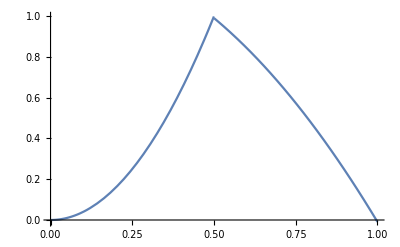

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
g[x_,n_]:=Nest[f,x,n]/2^(n-1)
```

```mathematica
g[x,2]
```

2 If[4 If[x>0&&x≤1/2,x^2,0.5-x^2/3-0.169]>0&&4 If[x>0&&x≤1/2,x^2,0.5-x^2/3-0.169]≤1/2,(4 If[x>0&&x≤1/2,x^2,0.5-x^2/3-0.169])^2,0.5-1/3 (4 If[x>0&&x≤1/2,x^2,0.5-x^2/3-0.169])^2-0.169]

```mathematica
(*Sawtooth Harmonics scale 2^(n-1)*)
```

```mathematica
w=Flatten[Table[{g[x,n],-g[x,n]},{n,8}]];
```

```mathematica
ga=Plot[w,{x,0,1},ImageSize->2000,PlotRange->All,AspectRatio->1];
```

General::munfl: (6.09553×10^-263)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Export["Qudratic_Sawtooth_Plus_Minus_Level8.jpg",ga]
```

Qudratic_Sawtooth_Plus_Minus_Level8.jpg

```mathematica
(*end*)
```